```mathematica
loadNotebook["inz_off_6_model.nb"];

wyliczSterowanie[wd_,w_,k1_]:=(
M= Inverse[D[w,{q[t]}].G2];
K1=k1*IdentityMatrix[3];
M=M.(D[wd,t]-K1.(w-wd));
M = M /.{l-> 0.1, R-> 0.03};
M
);

rozwiazRownania[M_,q0_,tmax_]:=(
pstrona = Transpose[G2.Transpose[{η[t]}]][[1]];
lstrona = D[q[t],t];
rownanie = Apply[Equal, Transpose[{lstrona, pstrona}],1];
tosolve = (rownanie /.{Subscript[η, 1][t] ->M[[1]], Subscript[η, 2][t]-> M[[2]],Subscript[η, 3][t]->M[[3]], l-> 0.1, R-> 0.03}) ~Join~ q0;
roz = NDSolve[tosolve, {x,y, Subscript[θ, 0],ϕ, θ,ψ}, {t,0,tmax}, Method->Automatic, MaxSteps->100000000];
roz
);

wyrysuj[rozwiazanie_, tmax_,anim_,i_]:=Module[{},
loc="C:\\Users\\Admin\\Documents\\GitHub\\hog\\Magisterka\\doc - off\\";

plot1=Plot[{x[t]-xd[t]/.rozwiazanie,y[t]-yd[t]/.rozwiazanie},{t,0,tmax},AxesLabel->{"t","e"},PlotLegends->Placed[{"e_x","e_y"},{0.90,0.75}],PlotRange->{-0.1,0.1}, PlotStyle->{Thick}];
plot1//Print;
Export[loc<>"inz_off_6_lin_"<>ToString[i]<>"_1.pdf",plot1];

plot2=Plot[wirowanie*t-ψ[t]/.rozwiazanie,{t,0,tmax},AxesLabel->{"t","e_ψ"},PlotRange->{-0.1,0.1}, PlotStyle->{Thick}];
plot2//Print;
Export[loc<>"inz_off_6_lin_"<>ToString[i]<>"_2.pdf",plot2];

zoomStart=12;
range=0.03;
xyMinMax={{zoomStart-range,zoomStart+range},{-30,30}};
g=Graphics[{EdgeForm[Thick],White,Disk[],Inset[Plot[Evaluate[{M[[1]]} /.rozwiazanie],{t,zoomStart-range,zoomStart+range},Axes->{True,False},ImageSize->140,Ticks->{{zoomStart-range,zoomStart,zoomStart+range},{-1,1}}]]},ImageSize->150];
(*plot3=Plot[Evaluate[{M[[1]]} /.rozwiazanie], {t,0,tmax}, PlotRange->All, AxesLabel->{"t","η_1"},Axes->{True, True},Epilog->{Transparent,EdgeForm[Thick],Rectangle[Sequence@@Transpose[xyMinMax]],Inset[Plot[Evaluate[{M[[1]]} /.rozwiazanie],{t,zoomStart-range,zoomStart+range},Frame->True,Axes->False,PlotRange->xyMinMax, Background->White],{30,0.5}]}];*)
plot3=Plot[Evaluate[{M[[1]]} /.rozwiazanie], {t,0,tmax}, PlotRange->All, AxesLabel->{"t","η_1"},Axes->{True, True},Epilog->{Inset[g,{40,35}]}];
plot3//Print;
Export[loc<>"inz_off_6_lin_"<>ToString[i]<>"_3.pdf",plot3];

(*data = Table[(M[[1]] /.rozwiazanie)[[1]],{t,0,tmax,1/10000}];
Periodogram[data,SampleRate->10000,PlotRange->All]//Print;*)

plot4=Plot[Evaluate[{M[[2]]} /.rozwiazanie], {t,0,tmax}, PlotRange->All, AxesLabel->{"t","η_2"},Axes->{True, True}];
plot4//Print;
Export[loc<>"inz_off_6_lin_"<>ToString[i]<>"_4.pdf",plot4];

plot5=Plot[Evaluate[{ϕ[t]} /.rozwiazanie], {t,0,tmax}, PlotRange->All, AxesLabel->{"t","ϕ"},Axes->{True, True}];
plot5//Print;
Export[loc<>"inz_off_6_lin_"<>ToString[i]<>"_5.pdf",plot5];

plot6=Plot[Evaluate[{θ[t]} /.rozwiazanie], {t,0,tmax}, PlotRange->All, AxesLabel->{"t","θ"},Axes->{True, True}];
plot6//Print;
Export[loc<>"inz_off_6_lin_"<>ToString[i]<>"_6.pdf",plot6];

plot7=Plot[Evaluate[{ψ'[t]} /.rozwiazanie], {t,0,tmax}, PlotRange->{495,505}, AxesLabel->{"t","ψ̇"},Axes->{True, True}];
plot7//Print;
Export[loc<>"inz_off_6_lin_"<>ToString[i]<>"_7.pdf",plot7];

krzywa1[t_] = {x[t] ,y[t]} /. rozwiazanie;

p1[t_] = ((Agms[x[t], y[t], Subscript[θ, 0][t]]/.rozwiazanie).Transpose[{{0,0,0,1}}]) /. {l-> 0.1, R-> 0.03};
x1[t_] = (p1[t])[[1,1,1]];
y1[t_] = (p1[t])[[1,2,1]];
krzywas[t_] = {x1[t], y1[t]} /. rozwiazanie;

p2[t_] = ((Agm2[x[t], y[t], Subscript[θ, 0][t]]/.rozwiazanie).Transpose[{{0,0,0,1}}]) /. {l-> 0.1, R-> 0.03};
x2[t_] = (p2[t])[[1,1, 1]];
y2[t_] = (p2[t])[[1,2, 1]];
krzywa2[t_] = {x2[t], y2[t]}/. rozwiazanie;

ẋ[t_] = (x1'[t] /.rozwiazanie)[[1]];
ẏ[t_] = (y1'[t] /. rozwiazanie)[[1]];
v[t_] = Re[Sqrt[(ẋ[t])^2+(ẏ[t])^2]];

krzywad[t_]={xd[t],yd[t]};

a1 = Animate[
Show[
{Plot[v[t], {t, 0, tmax}, PlotRange->All,AxesLabel->{"t","v"}]},
{
Graphics[{PointSize[Large],Red,Point[Dynamic[{t,v[t]}]]}]
}
],{t,0,tmax}];

curvs = ParametricPlot[{krzywas[t]}, {t, 0, tmax}, PlotRange->All, PlotStyle->{Red}, Axes->{True, True}, AxesOrigin->{0,0}];
curv1 = ParametricPlot[{krzywa1[t]}, {t, 0, tmax}, PlotRange->All,PlotStyle->{Blue}, Axes->{True, True},AxesOrigin->{0,0}];
curv2 = ParametricPlot[{krzywa2[t]}, {t, 0, tmax}, PlotRange->All,PlotStyle->{Yellow}, Axes->{True, True}, AxesOrigin->{0,0}];
curvd = ParametricPlot[{krzywad[t]}, {t, 0, tmax}, PlotRange->All,PlotStyle->{Black}, Axes->{True, True}, AxesOrigin->{0,0}];
plot8=ParametricPlot[{krzywa1[t],krzywad[t]},{t, 0, tmax},PlotRange->All,PlotStyle->{Red,Black}, Axes->{True, True}, AxesOrigin->{0,0}];
plot8//Print;
Export[loc<>"inz_off_6_lin_"<>ToString[i]<>"_8.pdf",plot8];


p11[t_]=Evaluate[{x[t],y[t]}/.rozwiazanie];
p22[t_]=Evaluate[{x2[t],y2[t]}/.rozwiazanie];
x11[t_]=(x[t]/.rozwiazanie)[[1]];
y11[t_]=(y[t]/.rozwiazanie)[[1]];
x22[t_]=(x2[t]/.rozwiazanie)[[1]];
y22[t_]=(y2[t]/.rozwiazanie)[[1]];
a2=Animate[
Show[
{curvs,curv1,curv2,curvd},
{
Graphics[{PointSize[0.03],Red,Point[Dynamic[p11[t]]]}],
Graphics[{PointSize[0.03], Red,Point[Dynamic[p22[t]]]}],
Graphics[{PointSize[0.02], Black,Point[Dynamic[{xd[t],yd[t]}]]}],
Graphics[
{Thickness[0.002],Green,
Line[
{
Dynamic[{x11[t],y11[t]}],
Dynamic[{x2[t],y2[t]}]
}
]
}]
}
],{t,0,tmax}];
If[anim,Print[a1],0];
If[anim,Print[a2],0];
0
];
```

```mathematica
M[[3]]//Simplify
```

500.+250. t-0.5 ψ[t]

0

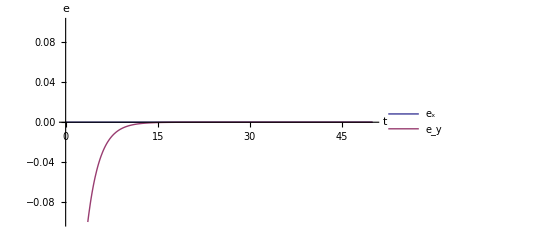

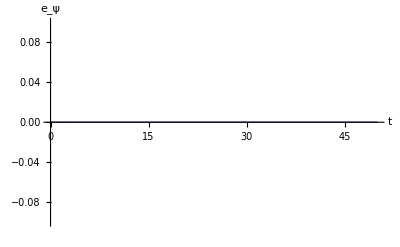

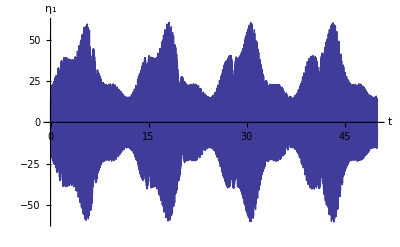

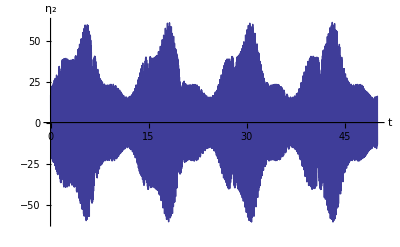

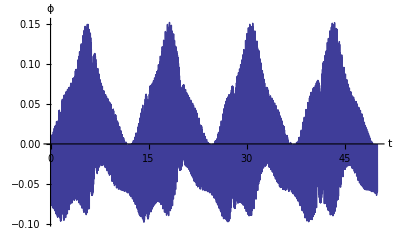

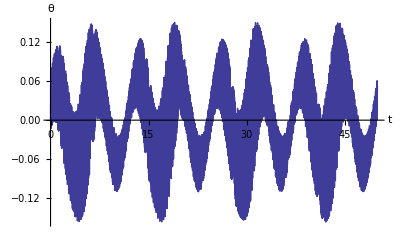

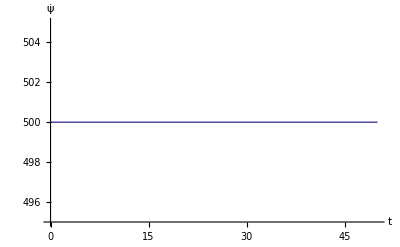

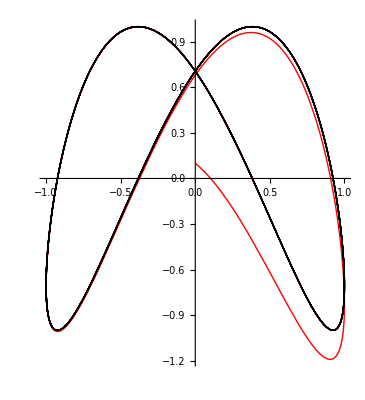

```mathematica
wirowanie = 500;
w={x[t],y[t],ψ[t]};
q0 = {x[0]== 0, y[0]==0.1, Subscript[θ, 0][0]==0, ϕ[0]==0, θ[0]==0, ψ[0]==0};(*,WhenEvent[ϕ[t]>1,ϕ[t]->0.9],WhenEvent[θ[t]>1,θ[t]->0.9], WhenEvent[ϕ[t]<-1,ϕ[t]->-0.9],WhenEvent[θ[t]<-1,θ[t]->-0.9]};*)
tmax = 50;
For[i=0,i<1,i++,
Print[i];
Which[i==0,{xd[t_],yd[t_]}=osemka[t,1],i==1,{xd[t_],yd[t_]}=kolo[t,3,1],i==2,{xd[t_],yd[t_]}=liniaX[t,3,1],True,{xd[t_],yd[t_]}=kwadrat[t,3,5]];
wd={xd[t],yd[t], wirowanie*t};
M = wyliczSterowanie[wd,w,0.5];
rozwiazanie = rozwiazRownania[M,q0,tmax];
wyrysuj[rozwiazanie, tmax,False,i];
];
```

```mathematica
data = Table[(Subscript[η, 1] /.rozwiazanie)[[1]],{t,0,tmax,1/10000}];
Periodogram[data,SampleRate->10000,PlotRange->All]//Print;
```

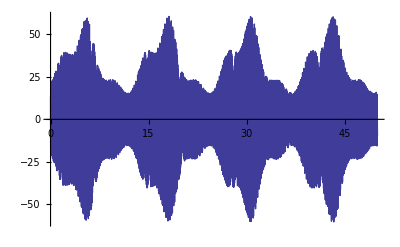

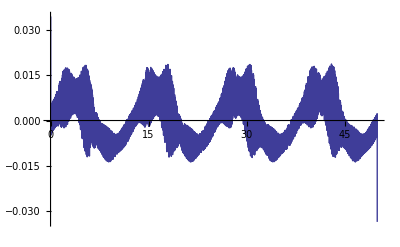

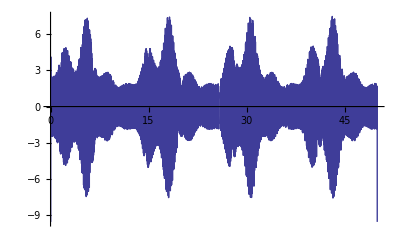

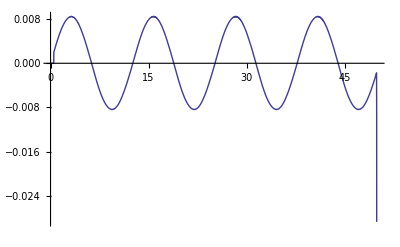

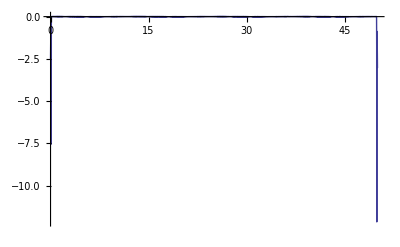

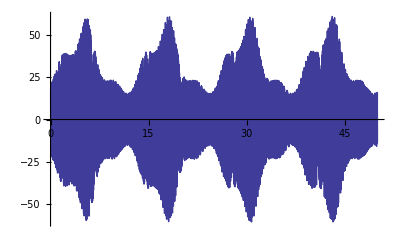

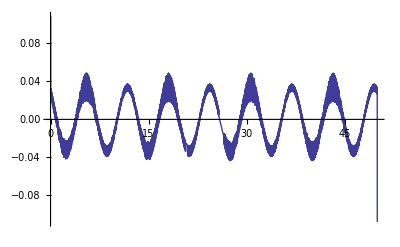

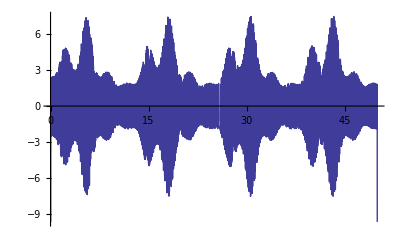

```mathematica
fun1[t_]=(ϕ[t]/.rozwiazanie)[[1]];
fun2[t_]=(M[[1]]/.rozwiazanie)[[1]];
data=Table[{t,fun2[t]},{t,0,tmax, 0.001}];
filteredData=LowpassFilter[Transpose[data][[2]],0.05];
filteredFunction=Interpolation[Transpose[{Transpose[data][[1]],filteredData}]];
Plot[fun2[t],{t,0,tmax}]
Plot[filteredFunction[t],{t,0,tmax}]
Plot[filteredFunction'[t],{t,0,tmax}]
data=Table[{t,filteredFunction[t]},{t,0,tmax, 0.001}];
filteredData=MeanFilter[Transpose[data][[2]],100];
filteredFunction2=Interpolation[Transpose[{Transpose[data][[1]],filteredData}]];
filteredFunction25[t_]=If[t<0.5,0,filteredFunction2[t]];
Plot[filteredFunction25[t],{t,0,tmax}]
Plot[filteredFunction2'[t],{t,0,tmax},PlotRange->All]


fun2[t_]=(M[[2]]/.rozwiazanie)[[1]];
fun1[t_]=(θ[t]/.rozwiazanie)[[1]];
data=Table[{t,fun2[t]},{t,0,tmax, 0.001}];
filteredData=LowpassFilter[Transpose[data][[2]],0.05];
filteredFunction=Interpolation[Transpose[{Transpose[data][[1]],filteredData}]];
Plot[fun2[t],{t,0,tmax}]
Plot[filteredFunction[t],{t,0,tmax}]
Plot[filteredFunction'[t],{t,0,tmax}]
data=Table[{t,filteredFunction[t]},{t,0,tmax, 0.001}];
filteredData=MeanFilter[Transpose[data][[2]],100];
filteredFunction3=Interpolation[Transpose[{Transpose[data][[1]],filteredData}]];
filteredFunction35[t_]=If[t<0.5,0,filteredFunction3[t]];
Plot[filteredFunction35[t],{t,0,tmax}]
Plot[filteredFunction3'[t],{t,0,tmax},PlotRange->All]
```

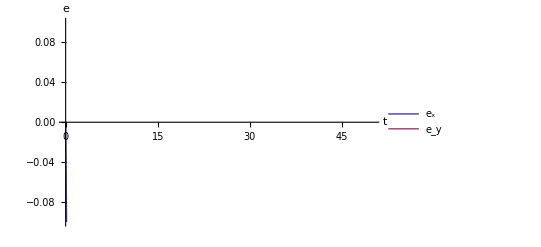

-Graphics-

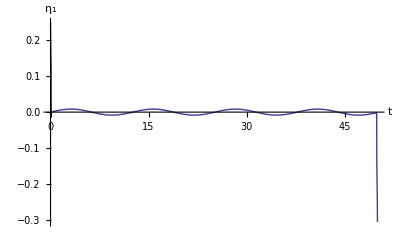

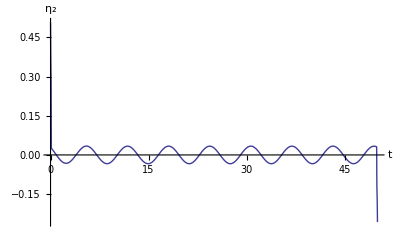

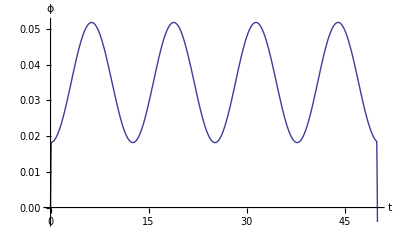

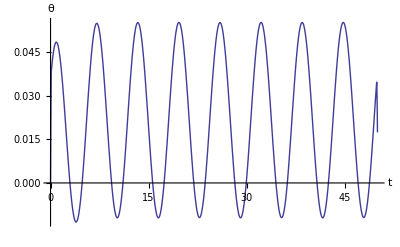

-Graphics-

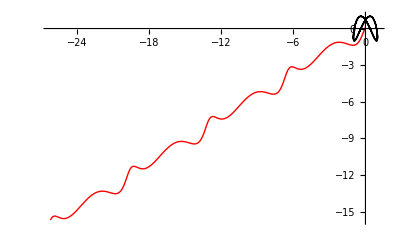

```mathematica
wirowanie = 500;
w={x[t],y[t],ψ[t]};
q0 = {x[0]== 0, y[0]==0.1, Subscript[θ, 0][0]==0, ϕ[0]==0, θ[0]==0, ψ[0]==0};
tmax = 50;
{xd[t_],yd[t_]}=osemka[t,1];
wd={xd[t],yd[t], wirowanie*t};
M = wyliczSterowanie[wd,w,0.5];
M[[1]]=filteredFunction2[t];
M[[2]]=filteredFunction3[t];
rozwiazanie = rozwiazRownania[M,q0,tmax];
wyrysuj[rozwiazanie, tmax,True,i];
```

InterpolatingFunction[{{0.,50.}},<>]

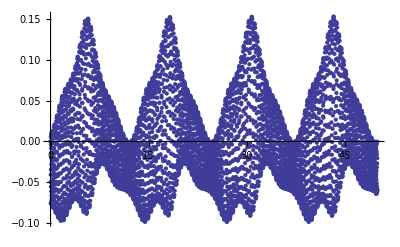

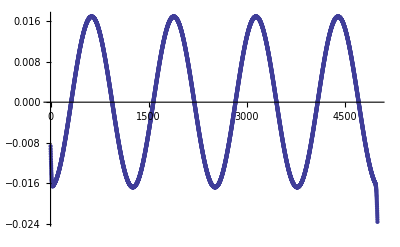

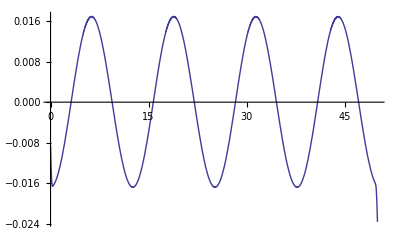

```mathematica
data=Table[{t,(ϕ[t]/.rozwiazanie)[[1]]},{t,0,tmax, 0.01}];
filteredData=LowpassFilter[Transpose[data][[2]],0.05];
filteredFunction=Interpolation[Transpose[{Transpose[data][[1]],filteredData}]];
ListPlot[data]
ListPlot[filteredData]
Plot[filteredFunction[t],{t,0,tmax}]
```